#### Definitions

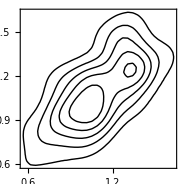
```mathematica
AllNeighbours=Dispatch[Rule@@@ReadList["AllNeighbours.txt"]];
MeaningAll=Dispatch[Rule@@@ReadList["MeaningAll8.txt"]];
b0=Mean[Normal[MeaningAll][[;;,2, ;;6]]];
a0=RandomReal[{0,.01},6];
humdata={{1.290034611362518,1.2041199826559248},{0.8450980400142568,1.146128035678238},{1.3010299956639813,1.4983105537896004},{1.,1.2304489213782739},{0.6989700043360189,0.8129133566428556},{1.0413926851582251,1.2041199826559248},{0.9777236052888477,0.9777236052888477},{0.9542425094393249,1.5185139398778875},{1.1613680022349748,0.9294189257142927},{1.423245873936808,1.3324384599156054},{1.1139433523068367,0.9030899869919435},{1.0791812460476249,1.},{1.2304489213782739,1.414973347970818},{1.0606978403536116,1.146128035678238},{0.9030899869919435,0.9542425094393249},{1.3117538610557542,1.1139433523068367},{1.3324384599156054,1.2671717284030137},{1.0969100130080565,0.7781512503836436},{1.8976270912904414,1.6580113966571124},{1.3710678622717363,1.255272505103306},{1.4313637641589874,1.2304489213782739},{1.1613680022349748,1.0413926851582251},{0.6020599913279624,0.8450980400142568},{1.2304489213782739,1.4313637641589874},{0.8750612633917001,0.9542425094393249},{1.1613680022349748,1.3617278360175928},{1.0969100130080565,1.0413926851582251},{1.255272505103306,1.1139433523068367},{0.9542425094393249,1.0413926851582251},{0.6020599913279624,0.6020599913279624},{1.,0.9777236052888477},{0.8129133566428556,0.9542425094393249},{1.3324384599156054,1.2174839442139063},{0.9542425094393249,1.1139433523068367},{1.2304489213782739,1.},{1.0413926851582251,0.8450980400142568},{1.1139433523068367,1.0791812460476249},{0.9030899869919435,0.9030899869919435},{1.6020599913279623,1.3010299956639813},{1.3010299956639813,1.2787536009528289},{0.9030899869919435,0.7403626894942439},{0.8450980400142568,1.2041199826559248},{0.7781512503836436,0.6020599913279624},{1.255272505103306,1.3424226808222062},{0.8450980400142568,0.8450980400142568},{1.,0.6989700043360189},{0.6989700043360189,0.7403626894942439},{1.,0.9030899869919435},{0.6989700043360189,0.7781512503836436},{1.,0.7781512503836436},{1.255272505103306,1.2671717284030137},{1.130333768495006,0.9030899869919435},{1.1760912590556813,1.255272505103306},{0.9777236052888477,0.7781512503836436},{0.9030899869919435,1.},{1.3617278360175928,1.255272505103306},{1.5797835966168101,1.380211241711606},{1.414973347970818,1.6020599913279623},{0.8129133566428556,0.9294189257142927},{0.7781512503836436,1.1139433523068367},{1.021189299069938,0.9542425094393249},{0.8129133566428556,0.9294189257142927},{0.9030899869919435,1.0413926851582251},{1.1903316981702914,1.1139433523068367},{1.2671717284030137,1.255272505103306},{0.9777236052888477,1.1760912590556813},{0.8450980400142568,0.8450980400142568},{1.3324384599156054,1.423245873936808},{1.146128035678238,1.146128035678238},{1.1139433523068367,0.9777236052888477},{1.0413926851582251,1.0791812460476249},{1.0413926851582251,0.9030899869919435},{1.290034611362518,1.0606978403536116},{1.3979400086720377,1.3424226808222062},{1.3222192947339193,1.7481880270062005},{1.2787536009528289,1.5563025007672873},{1.3617278360175928,1.1903316981702914},{1.3891660843645324,1.2041199826559248},{1.021189299069938,0.9777236052888477},{1.255272505103306,1.505149978319906},{1.1760912590556813,1.1760912590556813},{1.0791812460476249,1.146128035678238},{1.3710678622717363,1.255272505103306},{1.5563025007672873,1.3222192947339193},{0.6989700043360189,0.7781512503836436},{0.9030899869919435,1.146128035678238},{0.8450980400142568,0.6989700043360189},{1.0413926851582251,1.1760912590556813},{1.3424226808222062,1.021189299069938},{1.3010299956639813,1.462397997898956},{1.0413926851582251,1.130333768495006},{0.9030899869919435,0.8129133566428556},{1.,1.},{1.1139433523068367,1.4771212547196624},{0.6020599913279624,0.6020599913279624},{1.3424226808222062,1.},{1.5854607295085006,1.0413926851582251},{1.0413926851582251,0.9542425094393249},{1.3424226808222062,1.2304489213782739},{0.8450980400142568,0.9294189257142927}};
MCmedian=Log10@{{{9.,33.},{79.,45.5},{4.,7.},{4.,4.},{6.,4.},{21.,56.},{38.5,11.}},{{5.,5.5},{5.,6.},{5.,6.5},{6.,13.},{7.,5.},{7.,16.},{10.,5.},{12.5,6.},{13.,30.},{19.,36.},{22.,10.},{26.,40.},{38.,24.},{40.,20.}},{{6.5,8.5},{6.5,9.},{7.,7.},{7.,14.},{8.,5.5},{10.,6.},{18.,32.},{20.,31.5},{22.,10.5},{36.,21.}},{{7.,8.5},{8.,6.5},{8.,14.},{9.5,6.},{10.,17.},{13.5,8.},{14.5,8.5},{17.,10.},{17.,27.},{19.5,11.5},{20.,29.},{26.5,21.5},{27.,17.}}};
rrMedian=(MinMax/@(MCmedian[[2]]ᵀ));
cp=-Graphics-;
ℛ=ConvexHullMesh@cp[[1,1,Cases[cp,Line[x_]:>x,∞][[-1]]]];
rmfc=RegionMember@ℛ;
Show[cp,ListPlot@humdata,AspectRatio->Automatic]
```

#### Models

```mathematica
LeapsModelScaledGeneralFCD[alpha_,k_,smax_,seed_,ρ_,{w1_,w2_,w3_,w4_,w5_,w6_}]:=BlockRandom[SeedRandom[seed];
Module[{b,a,s,sm,μ},
μ=Dispatch[#[[1]]->ρ#[[2]]&/@MeaningAll];
b[0]=Mean[Normal[μ][[;;,2]]];
a[0]=a0;
s[0]=1;
sm[0]=s[0]/.μ;
a[i_]:=a[i]=(If[#<0.01,0.01,#]&/@(a[i-1]+k (a[i-1]^w1(sm[i-1]/b[i-1](a[i-1]/Total[a[i-1]])^w2)-a[i-1]^w3(a[i-1]/Total[a[i-1]])^w4)));
b[i_]:=b[i]=b[i-1]+UnitStep[a[i-1]-alpha] sm[i-1] a[i-1]^w5(a[i-1]/Total[a[i-1]])^w6;
s[i_]:=s[i]=If[Max[a[i-1]]>1,MaximalBy[#,(a[i-1].(#/.μ))&][[1]],RandomChoice@#]&@Complement[s[i-1]/.AllNeighbours,Table[s[j],{j,0,i-1}]];
sm[i_]:=sm[i]=s[i]/.μ;
{
Partition[Differences@Flatten[{0,SortBy[SortBy[DeleteCases[Sort[Split[Flatten@Position[#,_?(#>1&)],#2-#1<2&]],{}],Length][[-1]]&/@#,First][[;;,{1,-1}]]}],2],
Max[Flatten@#]>1,Max[Flatten@#]>alpha}&@Transpose[Table[a[i],{i,0,smax}]]]]
```

```mathematica
LeapsModelScaledFCD[alpha_,k_,smax_,seed_,ρ_]:=BlockRandom[SeedRandom[seed];
Module[{b,a,s,sm,μ},
μ=Dispatch[#[[1]]->ρ#[[2]]&/@MeaningAll];
b[0]=Mean[Normal[μ][[;;,2]]];
a[0]=a0;
s[0]=1;
sm[0]=s[0]/.μ;
a[i_]:=a[i]=(If[#<0.01,0.01,#]&/@(a[i-1]+k (sm[i-1]/b[i-1](a[i-1]/Total[a[i-1]])- a[i-1])));
b[i_]:=b[i]=b[i-1]+UnitStep[a[i-1]-alpha] sm[i-1]a[i-1];
s[i_]:=s[i]=If[Max[a[i-1]]>1,MaximalBy[#,(a[i-1].(#/.μ))&][[1]],RandomChoice@#]&@Complement[s[i-1]/.AllNeighbours,Table[s[j],{j,0,i-1}]];
sm[i_]:=sm[i]=s[i]/.μ;
{
Partition[Differences@Flatten[{0,SortBy[SortBy[DeleteCases[Sort[Split[Flatten@Position[#,_?(#>1&)],#2-#1<2&]],{}],Length][[-1]]&/@#,First][[;;,{1,-1}]]}],2],
Max[Flatten@#]>1,Max[Flatten@#]>alpha}&@Transpose[Table[a[i],{i,0,smax}]]]]
```

```mathematica
ModelFCD[{w1_,w2_,w3_,w4_,w5_,w6_}]:=TableForm@{a'==k (a^w1"s/b"("a/Σa")^w2-a^w3("a/Σa")^w4),b'==θ[a-α] a^w5 s("a/Σa")^w6}
```

```mathematica
LeapsModelScaledGeneralNoFCD[alpha_,k_,smax_,seed_,ρ_,{w1_,w2_,w3_,w4_,w5_,w6_}]:=BlockRandom[SeedRandom[seed];
Module[{b,a,s,sm,μ},
μ=Dispatch[#[[1]]->ρ#[[2]]&/@MeaningAll];
b[0]=Mean[Normal[μ][[;;,2]]];
a[0]=a0;
s[0]=1;
sm[0]=s[0]/.μ;
a[i$_] := a[i] = (If[#1 < 0.01, 0.01, #1] & ) /@ 
              (a[i- 1] + k(a[i-1]^w1 sm[i - 1](a[i- 1]/Total[a[i - 1]])^w2 - b[i - 1] a[i-1]^w3(a[i- 1]/Total[a[i - 1]])^w4)); 
b[i_] := b[i] = b[i - 1] + UnitStep[a[i - 1] - alpha] sm[i - 1] a[i-1]^w5*(a[i - 1]/Total[a[i- 1]])^w6; 
s[i_]:=s[i]=If[Max[a[i-1]]>1,MaximalBy[#,(a[i-1].(#/.μ))&][[1]],RandomChoice@#]&@Complement[s[i-1]/.AllNeighbours,Table[s[j],{j,0,i-1}]];
sm[i_]:=sm[i]=s[i]/.μ;
{
Partition[Differences@Flatten[{0,SortBy[SortBy[DeleteCases[Sort[Split[Flatten@Position[#,_?(#>1&)],#2-#1<2&]],{}],Length][[-1]]&/@#,First][[;;,{1,-1}]]}],2],
Max[Flatten@#]>1,Max[Flatten@#]>alpha}&@Transpose[Table[a[i],{i,0,smax}]]]]
```

```mathematica
LeapsModelScaledNoFCD[alpha_,k_,smax_,seed_,ρ_]:=BlockRandom[
SeedRandom[seed];
Module[{a,b,s,sm,μ},
μ=Dispatch[#[[1]]->ρ#[[2]]&/@MeaningAll];
b[0]=Mean[Normal[μ][[;;,2]]];
a[0]=a0;
s[0]=1;
sm[0]=s[0]/.μ;
a[i_]:=a[i]=(If[#<0.01,0.01,#]&/@(a[i-1]+k (sm[i-1](a[i-1]/Total[a[i-1]])-b[i-1] )));
b[i_]:=b[i]=b[i-1]+UnitStep[a[i-1]-alpha] sm[i-1];
s[i_]:=s[i]=If[Max[a[i-1]]>1,MaximalBy[#,(a[i-1].(#/.μ))&][[1]],RandomChoice@#]&@Complement[s[i-1]/.AllNeighbours,Table[s[j],{j,0,i-1}]];
sm[i_]:=sm[i]=s[i]/.μ;
{
Partition[Differences@Flatten[{0,SortBy[SortBy[DeleteCases[Sort[Split[Flatten@Position[#,_?(#>1&)],#2-#1<2&]],{}],Length][[-1]]&/@#,First][[;;,{1,-1}]]}],2],
Max[Flatten@#]>1,Max[Flatten@#]>alpha}&@Transpose[Table[a[i],{i,0,smax}]]]]
```

```mathematica
ModelNoFCD[{w1_,w2_,w3_,w4_,w5_,w6_}]:=TableForm@{a'==k (a^w1"s"("a/Σa")^w2-b a^w3("a/Σa")^w4),b'==θ[a-α] a^w5 s("a/Σa")^w6}
```

```mathematica
FractionalBrownianMotionProcessData=Table[
((Table[
LinearModelFit[Cases[#,{_Real,_Real}],{1,x},x,IncludeConstantBasis->True]["BestFitParameters"]&@With[{n=10^2,δt=.1,Tmax=30,σ=1,h=h1},
Table[Module[{trajectories},
trajectories=Abs[RandomFunction[FractionalBrownianMotionProcess[0,σ,h],{0,Tmax,δt},n]][[2,1]];
{Mean[Mean@#],√Total[(StandardDeviation@#)^2]}&@(N@{Mean[Length/@Select[#,#[[1]]==-1&]],Mean[Length/@Select[#,#[[1]]==1&]]}&/@Split/@Sign[trajectories-th])],{th,.5,2,.01}]
],2 10])ᵀ),
{h1,.1,0.45,.05}];
```

```mathematica
FractionalGaussianNoiseProcessData=Table[
((Table[
LinearModelFit[Cases[#,{_Real,_Real}],{1,x},x,IncludeConstantBasis->True]["BestFitParameters"]&@With[{n=5 10^2,δt=.1,Tmax=30,σ=1,h=h1},
Table[Module[{trajectories},
trajectories=Abs[RandomFunction[FractionalGaussianNoiseProcess[0,σ,h],{0,Tmax,δt},n]][[2,1]];
{Mean[Mean@#],√Total[(StandardDeviation@#)^2]}&@(N@{Mean[Length/@Select[#,#[[1]]==-1&]],Mean[Length/@Select[#,#[[1]]==1&]]}&/@Split/@Sign[trajectories-th])],{th,.5,2,.01}]],2 10])ᵀ),
{h1,.5,.95,.05}];
```

Data import and analysis

fcd

```mathematica
DataFCD=Import["FileNameFCD"];
```

```mathematica
ProcDataFCD=(Select[{#[[1]],N@Median[Cases[Join@@Select[#[[2,;;,1]],Length@#>1&],{_Integer..}]]}&@DeleteCases[DeleteCases[#,{_,False,_}|{_,True,False},∞],{___,_?(#<0&),___},∞]&/@#,Length@#[[2]]>1&])&/@DataFCD;
```

```mathematica
FCD=TableForm[
{#[[1]],#[[2]],#[[3]][ToString@Round[(#[[3]])/(#[[2]])100]<>"%"],#[[4]][ToString@Round[(#[[4]])/(#[[2]])100]<>"%"],#[[5]][ToString@Round[(#[[5]])/(#[[2]])100]<>"%"],#[[6]]}&/@SortBy[
{Panel@ModelFCD[#]&/@models,
Length/@DataFCD,
Length/@ProcDataFCD,
Length@Select[#,RegionMember[ImplicitRegion[.5<x<2&&.5<y<2,{x,y}],Log10@#[[2]]]&]&/@ProcDataFCD,
Length@Select[#,RegionMember[ℛ,Log10@#[[2]]]&]&/@ProcDataFCD,
If[NumberQ[#],Round[#,.001],0]&@If[#=={},0,RegionMeasure@RegionIntersection[ConvexHullMesh@#,ℛ]]&@Select[Log10@#[[;;,2]],rmfc]&/@ProcDataFCD}ᵀ,
{-#[[-1]]&,-#[[-2]]&}],
TableHeadings->{Automatic,{"Model","Total # Runs","# successful Runs","  # runs in \n HM bounding box","  # runs in\n HM Convex Hull","Vol(HM∩M)"}},
TableAlignments->Center]
```

nofcd

```mathematica
DataNoFCD=Import["FileNameNoFCD"];
```

```mathematica
ProcDataNoFCD=(Select[{#[[1]],N@Median[Cases[Join@@Select[#[[2,;;,1]],Length@#>1&],{_Integer..}]]}&@DeleteCases[DeleteCases[#,{_,False,_}|{_,True,False},∞],{___,_?(#<0&),___},∞]&/@#,Length@#[[2]]>1&])&/@DataNoFCD;
```

```mathematica
NoFCD=TableForm[
{#[[1]],#[[2]],#[[3]][ToString@Round[(#[[3]])/(#[[2]])100]<>"%"],#[[4]][ToString@Round[(#[[4]])/(#[[2]])100]<>"%"],#[[5]][ToString@Round[(#[[5]])/(#[[2]])100]<>"%"],#[[6]]}&/@SortBy[
{Panel@ModelNoFCD[#]&/@models,
Length/@DataNoFCD,
Length/@ProcDataNoFCD,
Length@Select[#,RegionMember[ImplicitRegion[.5<x<2&&.5<y<2,{x,y}],Log10@#[[2]]]&]&/@ProcDataNoFCD,
Length@Select[#,RegionMember[ℛ,Log10@#[[2]]]&]&/@ProcDataNoFCD,
If[NumberQ[#],Round[#,.001],0]&@If[#=={},0,RegionMeasure@RegionIntersection[ConvexHullMesh@#,ℛ]]&@Select[Log10@#[[;;,2]],rmfc]&/@ProcDataNoFCD}ᵀ,
{-#[[-1]]&,-#[[-2]]&}],
TableHeadings->{Automatic,{"Model","Total # Runs","# successful Runs","  # runs in \n HM bounding box","  # runs in\n HM Convex Hull","Vol(HM∩M)"}},
TableAlignments->Center]
```

function for calculating the AIC and BIC for a model  given the human behavioural data - humdata . 𝒟 is the smooth kernel distribution of the data generated by the model

```mathematica
Module[{𝒟,pdf,n=NumberPfParameters,k=SizeHumdata(*=100*)},
𝒟=SmoothKernelDistribution[data];pdf[{x_,y_}]:=PDF[𝒟,{x,y}];{(Log[100.] n)-2Total@Log[pdf/@humdata],(2n+(2 n^2+2 n)/(k-n-1))-2Total@Log[pdf/@humdata]}]
```